## Solving Multiple Elastic Pendulums

7/16/2020 Joshua Cheung

In this notebook, we simulate the motion of multiple, connected pendulum where the masses are connected by springs. Note that by choosing specific values for the masses and lengths of the pendulums, our program will simulate a single pendulum where the connecting spring also has mass.

### Define Constants

```mathematica
n =10;            (* Number of pendulums *)
g = 9.81;     (* Gravitational constant, in m/sec/sec *)
tfinal = 10;  (* Final time for the numerical solution *)
```

```mathematica
mass = .5;     (* Mass of pendulum in kg *)
mList = Table[mass, n];
mList[[n]] = 10;           (* Use this line to simulate a spring with mass *)

l0 = 1;        (* Resting length of a sinle spring *)
l0List = Table[l0, n];

k = 400;         (* Spring constant in N/m*)
kList = Table[k,n];
```

Initial Conditions

```mathematica
θ0 =π/4;   (* Initial angle of all pendulums *)
θ0List = Table[θ0,n];
(*θ0List =  {π/2, 3π/4, 175π/180};*)

ω0 = 0;         (* Initial angular velocity *)
ω0List=Table[ω0,n];

s0 = 0;           (* Distance stretched past L0 in m *)
s0List = Table[s0, n];

s0Prime = 0;      (* initial derivative of s *)
s0PrimeList = Table[s0Prime,  n];
```

### Determine Governing Equations

Let’s first define the θ’s and s’s as functions of time and their corresponding positions in Cartesian coordinates. Note that x and y are functions of θ and s in the mathematical sense.

```mathematica
θList[t_] = Table[θ[i][t], {i,n}];
sList[t_] = Table[s[i][t], {i,n}];

x[t_] = {(l0List[[1]]+sList[t][[1]])*Sin[θList[t][[1]]]};
Do[x[t_] = Append[x[t], x[t][[i-1]]+(l0List[[i]]+sList[t][[i]])*Sin[θList[t][[i]]]], {i,2,n}]
y[t_] = {-(l0List[[1]]+sList[t][[1]])*Cos[θList[t][[1]]]};
Do[y[t_] = Append[y[t], y[t][[i-1]]-(l0List[[i]]+sList[t][[i]])*Cos[θList[t][[i]]]],{i,2,n}]
```

Now let' s define the Lagrangian of our system : 	L = kinetic energy - potential energy

```mathematica
PESpring = Sum[1/2 kList[[i]] (s[i][t])^2,{i,n}];
PEGrav = Sum[mList[[i]]*g*y[t][[i]],{i,n}];
PE = PESpring + PEGrav;

KE = Sum[1/2 mass ((x'[t][[i]])^2+(y'[t][[i]])^2),{i,n}];
L = KE-PE;
```

Let' s define our system of governing equations using the Euler - Lagrange differential equation.
First, we’ll use the θ versions of the equation:      d/dt((δ L)/(δ θ')) - (δ L)/(δ θ) 	for every θ. 
We then add the s versions:  d/dt((δ L)/(δ s')) - (δ L)/(δ s) 	for every s

```mathematica
eqns[t_]={};
Do[eqns[t_]=Append[eqns[t],{D[D[L,θ[i]'[t]],t]-D[L,θ[i][t]] == 0}],{i,n}]
Do[eqns[t_]=Append[eqns[t],{D[D[L,s[i]'[t]],t]-D[L,s[i][t]] == 0}],{i,n}]
eqns[t_] = Flatten[eqns[t]];
```

Now, let’s add our initial conditions to our system of equations.

```mathematica
Do[eqns[t_]=Append[eqns[t],{θ[i][0]==θ0List[[i]], θ[i]'[0]==ω0List[[i]]}],{i,n}]
Do[eqns[t_]=Append[eqns[t],{s[i][0]==s0List[[i]], s[i]'[0]==s0PrimeList[[i]]}],{i,n}]
eqns[t_]=Flatten[eqns[t]];
```

### Numerically Solve ODE

```mathematica
solutions = NDSolve[eqns[t], {θList[t], sList[t]}, {t,0,tfinal}, Method -> {"EquationSimplification"->"Residual"}][[1]];
θSols[t_] = θList[t] /.solutions[[1]];
sSols[t_] = sList[t] /. solutions[[2]];
```

### Visualize Our Results

Plotting our results can be useful as a quick sanity check.

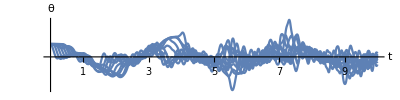

```mathematica
Plot[θSols[t], {t,0,tfinal}, PlotRange-> All, PlotStyle->Rainbow,AspectRatio->1/4, Ticks->{Range[tfinal],{-π,0,π/2, π,3π,5π,7π}}, AxesLabel->{"t","θ"}  ]
```

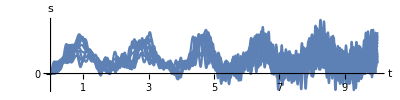

```mathematica
Plot[sSols[t], {t,0,tfinal}, PlotRange-> All, PlotStyle->Rainbow,AspectRatio->1/4, Ticks->{Range[tfinal],{0,.001,1, 5,10}}, AxesLabel->{"t","s"}  ]
```

Creating an animation. Again, we should first convert to Cartesian coordinates to make creating the animation easier.

```mathematica
xPos[t_] = {(l0List[[1]]+sSols[t][[1]])*Sin[θSols[t][[1]]]};
Do[xPos[t_] = Append[xPos[t], xPos[t][[i-1]]+(l0List[[i]]+sSols[t][[i]])*Sin[θSols[t][[i]]]], {i,2,n}]
yPos[t_] = {-(l0List[[1]]+sSols[t][[1]])*Cos[θSols[t][[1]]]};
Do[yPos[t_] = Append[yPos[t], yPos[t][[i-1]]-(l0List[[i]]+sSols[t][[i]])*Cos[θSols[t][[i]]]],{i,2,n}]
```

Now let’s make a list of all of our shapes to display

```mathematica
lines[t_] = {Line[{{0,0},{xPos[t][[1]], yPos[t][[1]]}}]};
Do[lines[t_]=Append[lines[t], Line[{{xPos[t][[i-1]], yPos[t][[i-1]]},{xPos[t][[i]], yPos[t][[i]]}}]],{i,2,n}]
```

```mathematica
massScale = (.2)/Max[mList];
disks[t_] = {{Blue, Disk[{xPos[t][[1]], yPos[t][[1]]}, massScale*mList[[1]]]}};
Do[disks[t_]= Append[disks[t],{Blue, Disk[{xPos[t][[i]], yPos[t][[i]]}, massScale*mList[[i]]]}], {i,2,n}]
```

```mathematica
shapes[t_] = Append[lines[t], disks[t]];
```

Finally, we can create the animation. Note that the bobs are sized proportionally to the largest mass.

```mathematica
windowSize = Sum[l0List[[i]],{i,n}]+2;    (* this depends heavily on the parameters and IC's probably need to hard code *)
Animate[Graphics[shapes[t], PlotRange->{{-windowSize-2, windowSize+2},{-windowSize-5, 3}}], {t,0,tfinal}, DefaultDuration-> tfinal]
```